```mathematica
location = "/home/jhell/research/results/1DTiO/1dEqm/runManagerTest3/1024/0.1/";
nMax = 18;
dataTable = Range[nMax];
For[i=0, i<nMax, i++, u=Import[location<>ToString[i]<>"/typeStats.dat", "Data" ]; MatrixPlot[u, ColorFunction->"GrayTones", ImageSize->{1024,1024}]  //Print]
```

-Graphics-

-Graphics-

-Graphics-

«15 more identical outputs»

```mathematica
~
```

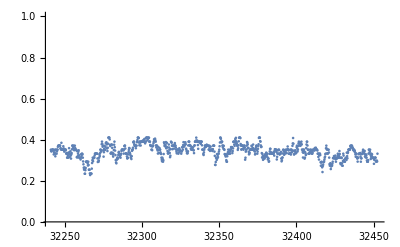

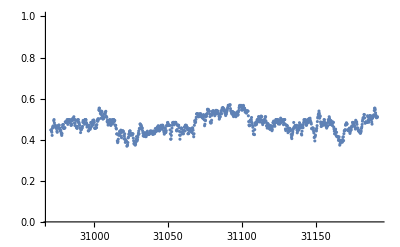

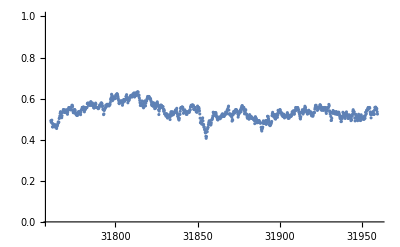

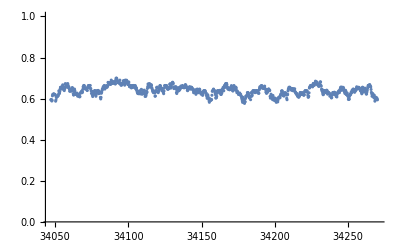

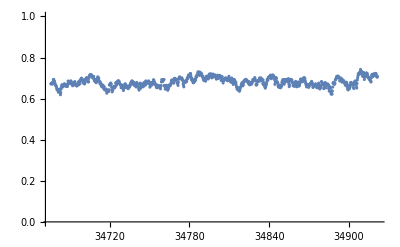

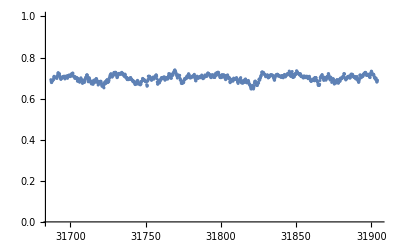

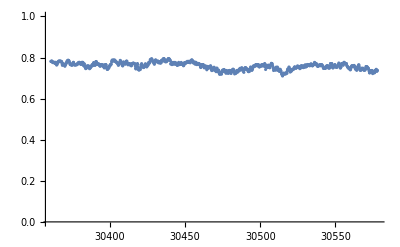

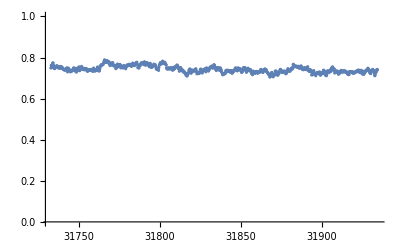

```mathematica
bondLocation = "/home/jhell/research/results/1DTiO/1dEqm/runManagerTest3/1024/0.1/";
nMax = 18;
dataTable = Range[nMax];
For[i=0, i<nMax, i++, u=Import[bondLocation<>ToString[i]<>"/numBonds.dat", "Data" ]; ListPlot[u, PlotRange->{0.0, 1.0}] //Print]
```

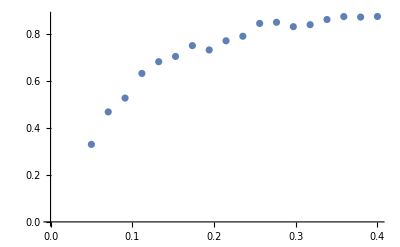

```mathematica
bondLocation = "/home/jhell/research/results/1DTiO/1dEqm/runManagerTest3/1024/0.1/";
nMax = 18;
dataTable = Range[nMax];
For[i=0, i<nMax, i++, u=Import[bondLocation<>ToString[i]<>"/extraInfo.dat", "Data" ]; dataTable[[i+1]] = {u[[1]][[1]], u[[1]][[3]]}];
ListPlot[dataTable]
```